# Грицак А.В. ПО-4 Лабораторная работа №2

## Задание 1

```mathematica
t1= (6*(x^2+1)*(x^2+y^2))/((2*x^2-1)*(x+y))+(x+y)^2+x^3+y^3
```

x^3+y^3+(x+y)^2+(6 (1+x^2) (x^2+y^2))/((-1+2 x^2) (x+y))

```mathematica
Expand[t1](*Expand раскрывает скобки в выражении*)
```

x^2+x^3+2 x y+y^2+y^3+(6 x^2)/((-1+2 x^2) (x+y))+(6 x^4)/((-1+2 x^2) (x+y))+(6 y^2)/((-1+2 x^2) (x+y))+(6 x^2 y^2)/((-1+2 x^2) (x+y))

```mathematica
ExpandAll[t1](*ExpandAll все раскрывает скобки в выражении ,даже если  в резульатате раскрытия в знаменателе остались скобки*)
(* ExpandAll их тоже раскроет*)
```

x^2+x^3+2 x y+y^2+y^3+(6 x^2)/(-x+2 x^3-y+2 x^2 y)+(6 x^4)/(-x+2 x^3-y+2 x^2 y)+(6 y^2)/(-x+2 x^3-y+2 x^2 y)+(6 x^2 y^2)/(-x+2 x^3-y+2 x^2 y)

```mathematica
Factor[t1] (*Factor представляет данный многочлена в виде произведения многочленов меньших степеней*)
```

1/((-1+2 x^2) (x+y))(6 x^2-x^3+5 x^4+2 x^5+2 x^6-3 x^2 y-x^3 y+6 x^4 y+2 x^5 y+6 y^2-3 x y^2+6 x^2 y^2+6 x^3 y^2-y^3-x y^3+2 x^2 y^3+2 x^3 y^3-y^4+2 x^2 y^4)

```mathematica
Together[t1](*Together складывает члены в сумму по общему знаменателю*)
```

1/((-1+2 x^2) (x+y))(6 x^2-x^3+5 x^4+2 x^5+2 x^6-3 x^2 y-x^3 y+6 x^4 y+2 x^5 y+6 y^2-3 x y^2+6 x^2 y^2+6 x^3 y^2-y^3-x y^3+2 x^2 y^3+2 x^3 y^3-y^4+2 x^2 y^4)

```mathematica
Apart[t1](*Apart записывает рациональное выражение в виде суммы членов с минимальными знаменателями*)
```

(x (-6-x-7 x^2+2 x^3+2 x^4))/(-1+2 x^2)+(2 (3-x+3 x^2+2 x^3) y)/(-1+2 x^2)+y^2+y^3+(12 (x^2+x^4))/((-1+2 x^2) (x+y))

```mathematica
Cancel[t1](*Cancel убирает общие множители в числителе и знаменателе выражения*)
```

x^3+y^3+(x+y)^2+(6 (1+x^2) (x^2+y^2))/((-1+2 x^2) (x+y))

```mathematica
Simplify[t1](*Simplify выполняет последовательность алгебраических и других преобразований выражения и возвращает простейшую форму*)
```

x^3+y^3+(x+y)^2+(6 (1+x^2) (x^2+y^2))/((-1+2 x^2) (x+y))

```mathematica
t2=Numerator[Together[t1]](*Numerator выводит числитель выражения*)
```

6 x^2-x^3+5 x^4+2 x^5+2 x^6-3 x^2 y-x^3 y+6 x^4 y+2 x^5 y+6 y^2-3 x y^2+6 x^2 y^2+6 x^3 y^2-y^3-x y^3+2 x^2 y^3+2 x^3 y^3-y^4+2 x^2 y^4

```mathematica
Collect[t2,x](*Collect собирает вместе члены выражения, включающие одинаковые степени х*)
```

2 x^6+6 y^2-y^3-y^4+x^5 (2+2 y)+x^4 (5+6 y)+x (-3 y^2-y^3)+x^3 (-1-y+6 y^2+2 y^3)+x^2 (6-3 y+6 y^2+2 y^3+2 y^4)

```mathematica
Collect[t2,y]
```

6 x^2-x^3+5 x^4+2 x^5+2 x^6+(-3 x^2-x^3+6 x^4+2 x^5) y+(6-3 x+6 x^2+6 x^3) y^2+(-1-x+2 x^2+2 x^3) y^3+(-1+2 x^2) y^4

```mathematica
Exponent[t2,x](*Выводит наибольшую степень икса*)
```

6

```mathematica
Exponent[t2,y]
```

4

```mathematica
Coefficient[t2,x,4](*Выводит коэффициент при x в четвертой степени*)
```

5+6 y

```mathematica
Coefficient[t2,y,4]
```

-1+2 x^2

## Задание 2

№1

```mathematica
D[x^n*Cos[x],x] (*D вычисляет производную выражения по иксу*)
```

n x^(-1+n) Cos[x]-x^n Sin[x]

№2

```mathematica
D[(a*x^3+2*x^2),x]
```

4 x+3 a x^2

```mathematica
D[(4*x^2-5*x+8-3/x),{x,3}](*D вычисляет производную выражения по иксу третьего порядка*)
```

18/x^4

```mathematica
D[(x^3*y^2+3*x^2),{x,3},{y,2}](*D вычисляет производную выражения по иксу третьего порядка и по игреку второго порядка*)
```

12

№3

```mathematica
Integrate[1/(x^2-1),x] (*находит интеграл по dx*)
```

1/2 Log[1-x]-1/2 Log[1+x]

№4

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Together[D[x^2/2-1/2*Log[1+x^2],x]]
```

x^3/(1+x^2)

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
ExpandAll[Together[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]]
```

1/(1+x^3)

№5

```mathematica
∫_1^4 (5*x - 2*√x + 32/x^3)ⅆx (*находит определенный интеграл по dx*)
```

259/6

№6

```mathematica
∫_0^1 (1 + x^4)^(1/3)ⅆx
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
∫_0^1. (1 + x^4)^(1/3)ⅆx
```

1.05753

## Задание 3

№1

```mathematica
Solve[a x^4 + x^2 + 3 == 0, x] (*решает уравнение или систему уравнений для перменной x, т.е. находит значения x*)
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

№2

```mathematica
Solve[x^2 + y == 1 && y^2 - x^2 == 2 , {x,y}] (*решает уравнение или систему уравнений для перменной x и y, т.е. находит значения x и y*)
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

№3

```mathematica
NSolve[x^2 - y^2 == 1 && y^3 + x == 5 , {x,y}] (*решает неравенство или систему неравенств для перменной x и y и находит численное решение, т.е. находит численные значения x и y*)
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

№4

```mathematica
z3 = DSolve[y'[x] - y[x]* Tan[x] == x, y[x],x] (*решает дифференциальное уравнение или систему уравнений для функции y[x] с независимой переменной x*)
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

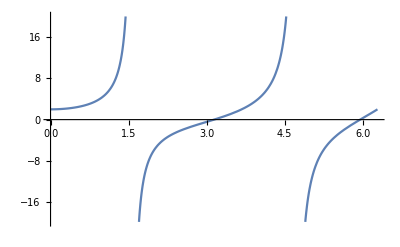

```mathematica
Plot[Evaluate[y[x] /. z3 /. {C[1]-> 1}] ,{x,0,2*Pi}]
(*Evuluate вычилсяет выражение даже если оно передано в качестве параметра*)
```

```mathematica
z2 = DSolve[y'[x] + y[x]* Tan[x] == 1/Cos[x], y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

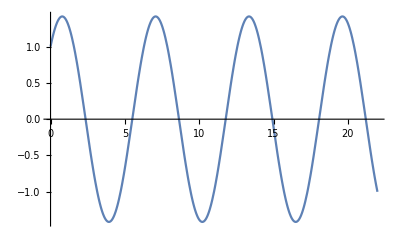

```mathematica
Plot[Evaluate[y[x] /. z2 /. {C[1]-> 1}] ,{x,0,7*Pi}]
```

№5

```mathematica
t7 = DSolve[{y''[x] - y'[x] + x y[x] == 0, y[0]==1, y'[0]==1}, y[x], {x, -7,7}]
```

{{y[x]→(ⅇ^(x/2) (((-1)^(2/3) AiryAi[-1/4 (-1)^(1/3)]+2 AiryAiPrime[-1/4 (-1)^(1/3)]) AiryBi[1/4 (-1)^(1/3) (-1+4 x)]-AiryAi[1/4 (-1)^(1/3) (-1+4 x)] ((-1)^(2/3) AiryBi[-1/4 (-1)^(1/3)]+2 AiryBiPrime[-1/4 (-1)^(1/3)])))/(2 AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-1/4 (-1)^(1/3)]-2 AiryAi[-1/4 (-1)^(1/3)] AiryBiPrime[-1/4 (-1)^(1/3)])}}

```mathematica
t8 = NDSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], {x, -7,7}]
```

{{y[x]→InterpolatingFunction[…][x]}}

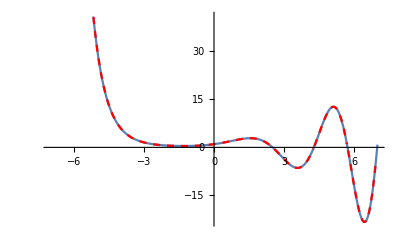

```mathematica
Show[Plot[ t8 [[1,1,2]],{x, -7,7}], Plot[t7[[1,1,2]], {x, -7,7},PlotStyle->{Dashed,Red}]]
```

## Задание 4.

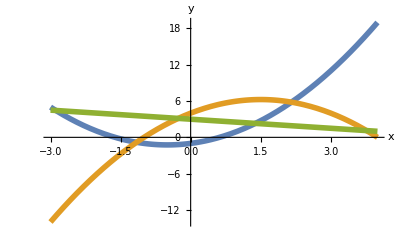

```mathematica
Plot[{x^2 + x - 1, -x^2 + 3*x + 4, -x/2 + 3}, {x, -3,4},PlotStyle->Thickness[0.01], AxesLabel->{"x", "y"}]
(* сторим графики заданных функций*)
```

```mathematica
eq1 = y == x^2 + x - 1 ;
eq2 = y == -x^2 + 3*x + 4;
eq3 = y == -x/2 + 3;
(*задаем уравнения прямых*)
```

```mathematica
sol1 = Solve[{eq1,eq3},{x,y}]
(*находим точку пересечения прямой и  парболы *)
```

{{x→1/4 (-3-√73),y→1/8 (27+√73)},{x→1/4 (-3+√73),y→1/8 (27-√73)}}

```mathematica
x1 = x /. sol1[[2]]
(*задаем первое грниченое значение (выбираем второе решение так как точка отрицательная )*)
```

1/4 (-3+√73)

```mathematica
sol2 = Solve[{eq2,eq3},{x,y}]
(*находим точку пересечения прямой и  парболы *)
```

{{x→1/4 (7-√65),y→1/8 (17+√65)},{x→1/4 (7+√65),y→1/8 (17-√65)}}

```mathematica
x2 = x /. sol2[[1]]
(*задаем второе грниченое значение (выбираем первое решение так как фигура находится выше праболы eq1 )*)
```

1/4 (7-√65)

```mathematica
sol3 = Solve[{eq1,eq2},{x,y}]
(*находим точку пересечения двух парабол *)
```

{{x→1/2 (1-√11),y→1/2 (5-2 √11)},{x→1/2 (1+√11),y→1/2 (5+2 √11)}}

```mathematica
x3 = x /. sol3[[2]]
(*задаем третье грниченое значение (выбираем второе решение)*)
```

1/2 (1+√11)

Разбиваем пластинку на маленькие кусочки площадью dxdy. Для определения площади пластинки складываем площади всех кусочков.

```mathematica
S = Integrate[1,{x,x1,x2}, {y, x^2 + x - 1 , -x/2 + 3}]*Integrate[1,{x,x2,x3},{y, x^2 + x - 1 , -x^2 + 3*x + 4}] //Simplify
```

((55+22 √11-√65) (-380+73 √65-73 √73))/1152

```mathematica
xc = 1/m*(Integrate[m/S*x,{x,x1,x2},{y, x^2 + x - 1 , -x/2 + 3}] + Integrate[m/S*x,{x,x2,x3},{y, x^2 + x - 1 , -x^2 + 3*x + 4}]) //Simplify
(*находим координату  x  центра масс пластинки*)
```

(3 (-4442+352 √11+455 √65+219 √73))/((55+22 √11-√65) (-380+73 √65-73 √73))

```mathematica
yc = 1/m*(Integrate[m/S*y,{x,x1,x2},{y, x^2 + x - 1 , -x/2 + 3}] + Integrate[m/S*y,{x,x2,x3},{y, x^2 + x - 1 , -x^2 + 3*x + 4}]) //Simplify
(*находим координату  y  центра масс пластинки*)
```

(3 (-2320+8800 √11+4875 √65-2263 √73))/(5 (55+22 √11-√65) (-380+73 √65-73 √73))

Сторим отдельно графики

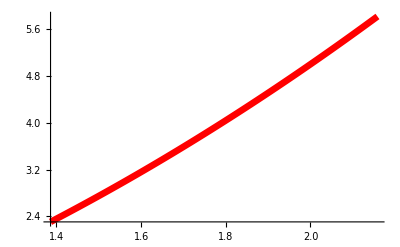
∞[-Graphics-]

```mathematica
p1 = Plot[ x^2 + x - 1, {x,x1,x3}, PlotStyle->{Thickness[0.012], RGBColor[1,0,0]}, DisplayFunction->Infinity]
```

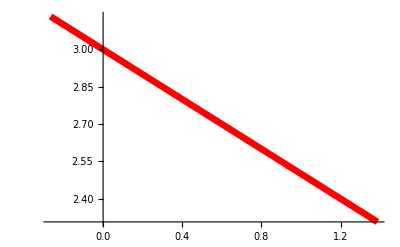
∞[-Graphics-]

```mathematica
p2 = Plot[ -x/2 + 3, {x,x1,x2}, PlotStyle->{Thickness[0.012], RGBColor[1,0,0]}, DisplayFunction->Infinity]
```

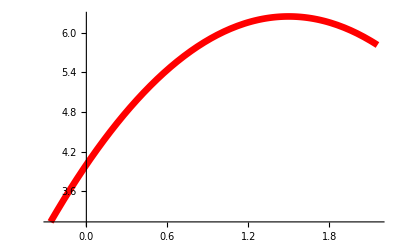
∞[-Graphics-]

```mathematica
p3 = Plot[  -x^2 + 3*x + 4, {x,x2,x3}, PlotStyle->{Thickness[0.012], RGBColor[1,0,0]}, DisplayFunction->Infinity]
```

```mathematica
Show[p1,p2,p3, AxesLabel-> {"x","y"}, Epilog -> { {PointSize[0.04], RGBColor[0,0,1], Point[{xc,yc}]}, Text[FontForm["C", {"Times-Bold",12}], {xc - 0.3, yc - 0.2}]},DisplayFunction-> $DisplayFunction]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[∞[-Graphics-],∞[-Graphics-],∞[-Graphics-],AxesLabel→{x,y},Epilog→{{PointSize[0.04],RGBColor[0, 0, 1],Point[{(3 (-4442+352 √11+455 √65+219 √73))/((55+22 √11-√65) (-380+73 √65-73 √73)),(3 (-2320+8800 √11+4875 √65-2263 √73))/(5 (55+22 √11-√65) (-380+73 √65-73 √73))}]},Text[FontForm[C,{Times-Bold,12}],{-0.436495,-0.7645}]},DisplayFunction→Identity]

Момент инерции отностильно оси :

```mathematica
Ix = Integrate[m/S y^2,{x,x1,x2},{y, x^2 + x - 1 , -x/2 + 3}]+ Integrate[m/S*y^2,{x,x2,x3},{y, x^2 + x - 1 , -x^2 + 3*x + 4}]//Simplify
```

(3 (-197288+401280 √11+224185 √65-66357 √73) m)/(56 (55+22 √11-√65) (-380+73 √65-73 √73))

```mathematica
Iy = Integrate[m/S x^2,{x,x1,x2},{y, x^2 + x - 1 , -x/2 + 3}]+ Integrate[m/S*x^2,{x,x2,x3},{y, x^2 + x - 1 , -x^2 + 3*x + 4}]//Simplify
```

(3 (-33420+5632 √11+10075 √65-4307 √73) m)/(10 (55+22 √11-√65) (-380+73 √65-73 √73))

```mathematica
Iz = Integrate[m/S*(x^2+y^2),{x,x1,x2},{y, x^2 + x - 1 , -x/2 + 3}]+ Integrate[m/S*(x^2+y^2),{x,x2,x3},{y, x^2 + x - 1 , -x^2 + 3*x + 4}]//Simplify
```

(3 (-1922200+2164096 √11+1403025 √65-452381 √73) m)/(280 (55+22 √11-√65) (-380+73 √65-73 √73))

```mathematica
II = Ix+Iy //Simplify
```

(3 (-1922200+2164096 √11+1403025 √65-452381 √73) m)/(280 (55+22 √11-√65) (-380+73 √65-73 √73))

```mathematica
II-Iz //Simplify
```

0